```mathematica
m[x_]=-s*(1/2-x)*x(1-x)
```

-s (1/2-x) (1-x) x

```mathematica
v[x_]=x*(1-x)/(2N)
```

((1-x) x)/(2 N)

```mathematica
G[x_]=Exp[-Integrate[2m[x]/v[x],x]]
```

ⅇ^(-2 N s (-x+x^2))

```mathematica
distribution[x_,s_,N_]=Integrate[G[q],{q,x,1}]/Integrate[G[q],{q,0,1}]/(v[x]*G[x])
```

(ⅇ^(2 N s (-x+x^2)) N (Erf[(√N √s)/(√2)]-Erf[(√N √s (-1+2 x))/(√2)]))/((1-x) x Erf[(√N √s)/(√2)])

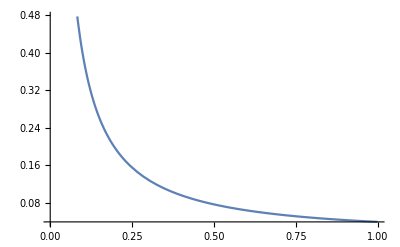

```mathematica
Plot[2*0.00001*distribution[x,0.0001,1000],{x,0.001,0.999}]
```